```mathematica
rulelist={30,110,54,120,180,240,225,154}
```

{30,110,54,120,180,240,225,154}

```mathematica
Data2=Flatten[Table[Table[Join[Flatten[CellularAutomaton[i,RandomInteger[1,8],16]],Flatten[Table[IntegerDigits[(2^(Position[rulelist,i]-1)),2,8],{m,1,5}]]],{j,1,10}],{i,rulelist}],1]
```

{{1,1,0,1,1,1,1,0,1,0,0,1,0,0,0,0,1,1,1,1,1,0,0,1,0,0,0,0,0,1,1,1,1,0,0,0,1,1,0,0,1,1,0,1,1,0,1,1,0,0,0,1,0,0,1,0,0,0,1,1,1,1,1,1,1,1,1,0,0,0,0,0,1,0,0,1,0,0,0,1,0,1,1,1,1,0,1,1,0,1,0,0,0,0,1,0,1,1,1,0,0,1,1,1,0,0,0,1,1,1,0,0,0,0,1,1,0,0,1,0,0,1,1,0,1,1,1,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1},{1,0,0,1,0,0,0,1,0,1,1,1,1,0,1,1,0,1,0,0,0,0,1,0,1,1,1,0,0,1,1,1,0,0,0,1,1,1,0,0,0,0,1,1,0,0,1,0,0,1,1,0,1,1,1,1,0,1,0,0,1,0,0,0,1,1,1,1,1,1,0,0,1,0,0,0,0,0,1,1,0,1,0,0,0,1,1,0,1,1,1,0,1,1,0,1,0,0,0,0,1,0,0,1,1,0,0,1,1,1,1,1,0,1,1,1,0,0,0,0,1,1,0,0,1,0,0,0,1,0,1,1,1,1,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1},«77»,{0,1,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,1,0,0,0,1,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0}}

```mathematica
Data2//Dimensions
```

{80,176}

```mathematica
catest1=Join[Flatten[CellularAutomaton[30,RandomInteger[1,8],16]],Flatten[Table[IntegerDigits[30,2,5],{m,1,5}]]]
```

{0,1,1,1,0,1,0,0,1,1,0,0,0,1,1,0,1,0,1,0,1,1,0,0,1,0,1,0,1,0,1,1,0,0,1,0,1,0,1,0,0,1,1,0,1,0,1,1,0,1,0,0,1,0,1,0,1,1,1,1,1,0,1,1,0,0,0,0,0,0,1,0,0,0,0,0,0,1,1,1,1,0,0,0,1,1,0,0,1,1,0,1,1,0,1,1,0,0,0,1,0,0,1,0,0,0,1,1,1,1,1,1,1,1,1,0,0,0,0,0,1,0,0,1,0,0,0,1,0,1,1,1,1,0,1,1,1,1,1,1,0,1,1,1,1,0,1,1,1,1,0,1,1,1,1,0,1,1,1,1,0}

```mathematica
{161}
```

{161}

```mathematica
Export["CA2.txt",Data2]
```

CA2.txt

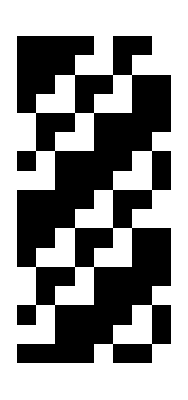

```mathematica
CellularAutomaton[154,RandomInteger[1,8],16]//ArrayPlot
```

```mathematica
30,110,54,120,180,240,225,154
```

```mathematica
ArrayPlot[Data
```

```mathematica
Export["CA1.txt",Data1]
```

CA1.txt

```mathematica
Data1[[1]]//Dimensions
```

{222}

```mathematica
h1=SampleHidden[W][Data1[[1]]];
h2=SampleHidden
```

```mathematica
CA2W=Import["weights.tsv"]
```

{{-3.38043,-0.659295,-6.27014,1.51454,6.51906,-3.49,2.0086,-6.06971,-3.04343,-2.50324,2.25902,2.8881,-0.094694,-0.827887,4.95917,«42570»,-2.54733,-0.780948,0.23894,1.55563,1.13245,2.14594,-0.015035,0.502814,-1.05245,-0.503753,0.133984,0.458266,1.29326,-0.662456,0.134198}}

```mathematica
CA2W//Dimensions
```

{1,42600}

```mathematica
Ce
```